-Graphics-

# Data Science

## How to Reshape Data

-Graphics-

## Built-in Data Structures

List

Association

## Association

Association is Like a List, but You Use Keys to Refer to Values instead of Numbers

```mathematica
{1, 2, 3}[[2]]
```

2

```mathematica
<|"a" -> 1, "b" ->2, "c" -> 3|>[["a"]]
```

1

Part Extraction

```mathematica
data = {<|"a"-><|"a"->"a1"|>,"b"-><|"b"->"b1"|>|>, <|"a"-><|"a"->"a2"|>,"b"-><|"b"->"b2"|>|>};
data[[All, All, "a"]]
```

{<|a→a1,b→Missing[KeyAbsent,a]|>,<|a→a2,b→Missing[KeyAbsent,a]|>}

Functions Specifics for Association

```mathematica
Keys[<|"a" -> 1|>]
```

```mathematica
Values[<|"a" -> 1|>]
```

```mathematica
Lookup[<|"a" -> 1|>, "a"]
```

```mathematica
KeyTake[<|a->1,b->2,c->3|>,{a,b}]
```

```mathematica
KeyDrop[<|a->1,b->2|>,a]
```

```mathematica
KeyValueMap[f,<|a->1,b->2,c->3|>]
```

```mathematica
MapIndexed[f,<|a->1,b->2,c->3|>]
```

<|a→f[1,{Key[a]}],b→f[2,{Key[b]}],c→f[3,{Key[c]}]|>

```mathematica
Merge[{<|a->1,b->2|>,<|b->4,c->5|>},Identity]
```

<|a→{1},b→{2,4},c→{5}|>

```mathematica
Merge[{<|a->1,b->2|>,<|a->5,b->10|>},Total]
```

<|a→6,b→12|>

## Importing Sample Data

Create Data on Your Machine

```mathematica
folder = FileNameJoin[{NotebookDirectory[], "data"}];
CreateDirectory[folder];

data = ;

Export[
FileNameJoin[{folder, "persons.csv"}] ,
Join[{Keys@First@data}, Values @ data]
]

SeedRandom[1];

users = data[[All, "id"]];
probs = AssociationMap[RandomSample@Table[i^8, {i, Length[users]}]&,users];

transactions = Table[
Export[
FileNameJoin[{folder, "2016-10-" <> ToString[i]<>".csv"}],
Join[
{{"from", "to", "amount"}},
Table[
With[{u = RandomChoice[users]}, {u, RandomChoice[probs[u] -> Range[Length[users]]]}] ~ Join ~ {ToString @ AccountingForm[RandomReal[{1000, 4000}],NumberPoint->",", NumberSeparator -> ".", DigitBlock->3]},
{j, RandomInteger[{5, 15}]}
]
]
], 
{i, 30}
];
```

/Users/rdv/Dropbox (Wolfram)/SS2019/data/persons.csv

Manually Inspect Data

```mathematica
SystemOpen[folder]
```

Import the Data

```mathematica
data = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]]
```

## Possible Representations

Lists of Lists

```mathematica
{
{1,"Deanna Gardner","F",30,57,167,"ECP-8254"},
{2,"Brian Rodriguez","M",42,71,174,"50BH7"}
}
```

{{1,Deanna Gardner,F,30,57,167,ECP-8254},{2,Brian Rodriguez,M,42,71,174,50BH7}}

Association of Lists

```mathematica
<|
"full_name"->{"Rebecca Burke","Brian Taylor","Heather Watkins","Chris Villegas"},
"sex"->{"F","M","F","M"}
|>
```

<|full_name→{Rebecca Burke,Brian Taylor,Heather Watkins,Chris Villegas},sex→{F,M,F,M}|>

List of Associations

```mathematica
{
<|"sex"->"F","full_name"->"Deanna Gardner"|>,
<|"sex"->"M","full_name"->"Brian Rodriguez"|>,
<|"sex"->"F","full_name"->"Rebecca Burke"|>
}
```

{<|sex→F,full_name→Deanna Gardner|>,<|sex→M,full_name→Brian Rodriguez|>,<|sex→F,full_name→Rebecca Burke|>}

## Lists of Lists

```mathematica
csv = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
data = Rest @ csv
```

```mathematica
data[[All, 2]]
```

```mathematica
Rule @@@ data[[All, {2, 4}]]
```

Advantages

Very small size for large data.

Efficient structure.

Disadvantages

Your code is unreadable.

## Association with Lists

```mathematica
csv = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
headers = First@csv;
data = Rest @ csv;
```

```mathematica
grouped = AssociationThread[headers -> Transpose[data]]
```

```mathematica
grouped[[{"id", "sex"}, 1]]
```

```mathematica
grouped[[{"fullname", "sex"}, {3, 4, 5, 6}]]
```

Advantages

Code is now readable; you can now refer to columns in the code.

Efficient structure.

Disadvantages

Working with list of arrays might be counterintuitive.

#### Rollback to list of lists

```mathematica
Values @ grouped
```

## Lists of Association

```mathematica
csv = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
headers = First@csv;
data = Rest @ csv;
```

### Method 1

```mathematica
grouped = Map[AssociationThread[headers -> #] &, data]
```

### Method 2

```mathematica
grouped =Transpose[AssociationThread[headers -> Transpose[data]], AllowedHeads->All]
```

```mathematica
grouped[[All, "sex"]]
```

{F,M,F,M,F,M,F,M,F,M,F,M,F,M,F,M,F,M,F,M}

```mathematica
grouped[[All, {"sex", "fullname"}]]
```

Advantages

You can still think in terms of lists of lists.

Disadvantages

Can be memory inefficient for very large datasets.

### Rollback to list of lists

```mathematica
Values @ grouped
```

## Merging Multiple CSV Files

```mathematica
SystemOpen[folder]
```

```mathematica
names = FileNames["2016-*.csv", folder];
```

```mathematica
Map[FileBaseName[#] &, names]
```

{2016-10-10,2016-10-11,2016-10-12,2016-10-13,2016-10-14,2016-10-15,2016-10-16,2016-10-17,2016-10-18,2016-10-19,2016-10-1,2016-10-20,2016-10-21,2016-10-22,2016-10-23,2016-10-24,2016-10-25,2016-10-26,2016-10-27,2016-10-28,2016-10-29,2016-10-2,2016-10-30,2016-10-3,2016-10-4,2016-10-5,2016-10-6,2016-10-7,2016-10-8,2016-10-9}

```mathematica
Interpreter["StructuredDate"][Map[FileBaseName, names]]
```

```mathematica
Map[StringSplit[FileBaseName@#, "-"] &, names]
```

```mathematica
dates = Map[DateObject[FromDigits /@ StringSplit[FileBaseName[#], "-"]] &, names];
```

```mathematica
reshape[csv_String] := reshape[Import[csv, "CSV"]]
reshape[csv_List] := With[
{headers = First[csv], data = Rest[csv]},
Transpose[AssociationThread[headers -> Transpose[data]], AllowedHeads->All]
]
```

```mathematica
transactions = Apply[
Function[
{date, csv},
reshape[csv]
],
Transpose[{dates, names}],
{1}
];
```

```mathematica
transactions = Flatten @ Apply[
Function[
{date, csv},
Map[Append[#, "date" -> date]&,reshape[csv]]
],
Transpose[{dates, names}],
{1}
]
```

```mathematica
fixAmount[s_String] := ToExpression@StringReplace[s,{ "." -> "",  "," -> "."}]
fixAmount[s_] := s
```

```mathematica
transactions = Flatten @ Apply[
Function[
{date, csv},
Map[Append[#, {"date" -> date, "amount" -> fixAmount[#amount]}]&,reshape[csv]]
],
Transpose[{dates, names}],
{1}
];
```

## Merging All Data

```mathematica
transactions;
```

```mathematica
persons = reshape[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
getTransactions[id_, key_:"from"] := 
Select[
transactions, 
Function[
{t},
id == t[key]
]
]
```

```mathematica
merged = Map[
Append[
#, {
"outgoing" -> getTransactions[#id, "from"],
"incoming" -> getTransactions[#id, "to"]
}
] &,
persons
];
```

## Querying the Data

```mathematica
Dataset @ merged
```

Dataset[<>]

```mathematica
merged[[1]]
```

```mathematica
merged[[1, "outgoing", All, "amount"]]
```

{142852,317039,313452,384.59,210846,206385,118236,335.76,284607,168534,222878,212134,244797,137689,213.31,335689,329873,264.82,344055,308475}

```mathematica
PieChart[
Map[
Total[#[["outgoing", All, "amount"]]]&,
merged
],
ChartLabels->merged[[All, "fullname"]]
]
```

-Graphics-

## Example Graph

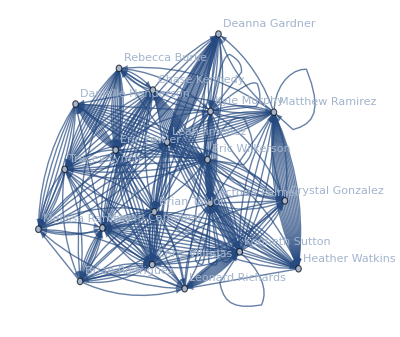

```mathematica
makeGraph[tr_] := Graph[
Map[
Labeled[#id, #["fullname"]] &,
persons
],
Map[
#from -> #to &,
tr
]
]
makeGraph[transactions]
```

```mathematica
Manipulate[
makeGraph[Select[transactions,#date === i &]],
{i, DeleteDuplicates[transactions[[All, "date"]]]},
ControlType->Slider
]
```

```mathematica
regroup = GroupBy[transactions, Key["date"]];
Manipulate[
makeGraph[regroup[i]],
{i, Keys[regroup]},
ControlType->Slider
]
```

```mathematica
regroup = GroupBy[transactions, Key["date"], makeGraph];
Manipulate[
regroup[i],
{i, Keys[regroup]},
ControlType->Slider
]
```

```mathematica
regroup = GroupBy[transactions, Key["from"], makeGraph];
Manipulate[
regroup[i],
{i, Keys[regroup]},
ControlType->Slider
]
```